# Properties of Trig Functions.

#### DEFINITIONS: Sin[x] = (ⅇ^ⅈx - ⅇ^-ⅈx)/(2ⅈ) Cos[x] =(ⅇ^ⅈx + ⅇ^-ⅈx)/2 where ⅈ≡√-1

#### Therefore, the inverse can be written as ⅇ^ⅈx = Cos[x] + ⅈ Sin[x] ⅇ^-ⅈx = Cos[x] - ⅈ Sin[x]

#### Values at the origin Sin[0]=0 Cos[0]=1

#### Derivatives ∂_x Sin[x]=Cos[x] ∂_x Cos[x]=-Sin[x]

```mathematica
D[Sinh[x], x]
```

Cosh[x]

```mathematica
D[Cosh[x], x]
```

Sinh[x]

#### Identity Cos[x]^2+ Sin[x]^2=1

```mathematica
Simplify[Cosh[x]^2-Sinh[x]^2]
```

1

#### Plots of Sin, Cos, and Tan

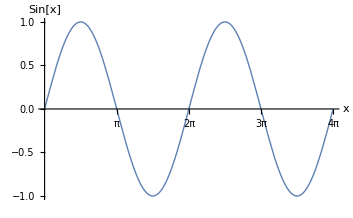

```mathematica
Plot[Sin[x],{x,0,4π},AxesLabel->{"x","Sin[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks->{{{π,"π"},{2π,"2π"},{3π,"3π"},{4π,"4π"}},Automatic}]
```

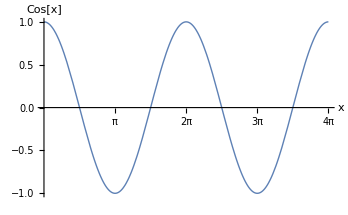

```mathematica
Plot[Cos[x],{x,0,4π},AxesLabel->{"x","Cos[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick,Ticks->{{{π,"π"},{2π,"2π"},{3π,"3π"},{4π,"4π"}},Automatic}]
```

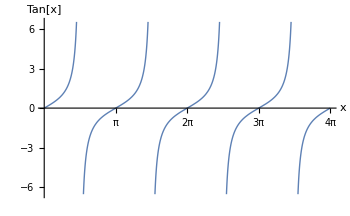

```mathematica
Plot[Tan[x],{x,0,4π},AxesLabel->{"x","Tan[x]"},BaseStyle->{FontSize->18},PlotStyle->Thick,Exclusions->{Cos[x]==0},Ticks->{{{π,"π"},{2π,"2π"},{3π,"3π"},{4π,"4π"}},Automatic}]
```